# Solving the Radial Schrödinger equation using B-Polynomials via the Galerkin Method

## Report of Progress

Andrew Senchuk

Department of Physics and Astronomy, The University of Manitoba

November, 2013

## Introduction

This report will describe the progress made in generating wavefunctions for the Dirac equation in Hydrogen-like (H-like) ions where the nucleus is not a point.  As a preliminary step, the schrodinger equation for a H-like ion with a point nucleus was solved via the Galerkin method using the so-called B (or Bernstein) - polynomials as basis functions.  This report will not describe the Galerkin method itself; that introduction can be found in a separate report.  We begin the present discussion with a review of the Schrödinger equation for a single electron in a central potential V (r). First, we decompose the Schrodinger wave function in spherical coordinates and discuss the equation governing the radial wave function. Following this, we consider analytical solutions to the radial Schrödinger equation for the special case of a Coulomb potential. The analytical solutions provide a guide for our later numerical analysis. This is followed by a discussion of the numerical solution to the radial Schrödinger equation via the Galerkin method using a B-polynomial basis. Afterwards, some analysis is made on the accuracy of the numerical solutions compared with the analytical solutions.  Specifically we consider the residuals as a function of B-polynomial order, which gives us a quantitative measure of sufficient order inclusion.

## Radial Schrödinger Equation

The basic equation for our subsequent numerical studies is the radial Schrödinger equation with the separation constant λ = ℓ(ℓ + 1):

(ⅆ^2 P)/(ⅆ r^2)+(2m)/ℏ^2(E -V(r) - (ℓ(ℓ+1)ℏ^2)/(2 mr^2))P=0

and V(r) is the nuclear potential V_nuc(r):

V_nuc(r)=-Ze^2/(4 πϵ_0)1/r

To facilitate calculations we will work in Atomic units, which allow us to be rid of unnecessary physical constants.  Atomic units are defined by requiring that the electron’s mass m, the electron’s charge |e|/√(4 πϵ_0), and Planck’s constant ℏ, all have value 1.  The atomic unit of length is the Bohr radius a_0= 4 πϵ_0 ℏ^2/me^2 = 0.529177.. A^◦ and the atomic unit of energy is me^4/(4 πϵ_0 ℏ)^2 = 27.2114 . . . eV.  In atomic units, the radial Schrödinger equation (1) becomes

(ⅆ^2 P(r))/(ⅆ r^2)+2(E -V(r) - (ℓ(ℓ+1))/(2 r^2))P(r)=0

We seek solutions to (3) that satisfy the normalization condition

∫_0^∞ P^2(r)ⅆr=1

The solution of this equation can be found in Johnson (2007).  We find the energy eigenvalue equation to be

E_n=-Z^2/(2 n^2)

There are n distinct radial wave functions corresponding to E_n.  These functions are P_nℓ(r)with ℓ = 0, 1,..., n-1, and are given in terms of a confluent hypergeometric series:

P_nℓ(r)=1/(n(2ℓ+1)!)√((Z (n+ℓ)!)/((n-ℓ-1)!))((2Z r)/n)^(ℓ+1)ⅇ^(-Z r/n) F(-n+ℓ+1,2ℓ+2,2Z r/n)

The lowest few states are found to be:

P_10=2 Z^(3/2) x ⅇ^(-Z x);
	P_20=1/(√2) Z^(3/2) x ⅇ^(-Z x/2) (1-1/2 Z x);
P_21=1/(2 √6) Z^(5/2) x^2 ⅇ^(-Z x/2);
P_30=2/(3 √3) Z^(3/2) x ⅇ^(-Z x/3) (1-2/3 Z x+2/27 Z^2 x^2);
P_31=8/(27 √6) Z^(5/2) x^2 ⅇ^(-Z x/3) (1-1/6 Z x);
P_32=4/(81 √30) Z^(7/2) x^3 ⅇ^(-Z x/3);

Graphically, these are are shown in the figure below:

## B (Bernstein) - Polynomial Basis Sets for approximate solutions

The main goal is to present a solution of the Schrödiger equation on a closed interval [a, b] with continuous polynomials which require no particular knot (or grid) sequence.  To that end, we introduce the so-called Bernstein, or B-polynomials of degree n, B_(n,i)(r), which are defined as:

```mathematica
BPolynomial[n_,i_,a_,b_,x_]:=Binomial[n,i]((x-a)^i (b-x)^(n-i))/(b-a)^n ;
```

for i = 0, 1, ..., n and Binomial[n,i] is the binomial coefficient, given by:

```mathematica
?Binomial
```

RowBox[{"Binomial", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["m", "TI"]}], "]"}] gives the binomial coefficient RowBox[{"(", GridBox[{{StyleBox["n", "TI"]}, {StyleBox["m", "TI"]}}], ")"}].

Thus, there are only (n+1) nth-degree polynomials.  For convenience, we set B_(n,i)(r) = 0, if i < 0 or i > 0.  We can view all the non-vanishing B-polynomials of degree n supported over the interval.  The first and last polynomials are generally related to the boundary conditions of the problem currently under consideration.  As an example, a set of 6 B-polynomials of degree 5 over the interval [-1,1] is shown here:

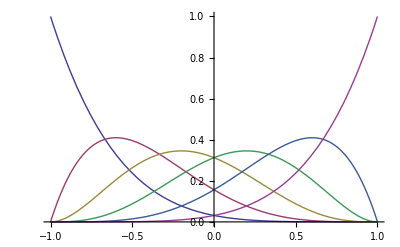

```mathematica
Plot[Evaluate[Table[BPolynomial[5,k,-1,1,x],{k,0,5}]],{x,-1,1}]
```

It is clear, that all the B-polynomials are positive and the sum of all the polynomials is equal to 1 at any point x.

## Solving the Radial Schrödinger equation using B-polynomials

Our ultimate goal is to evaluate MBPT expressions for the correlation energy.  As an aid we introduce a discrete basis set and, thereby, reduce the infinite sums and integrals over the real spectrum to finite sums over a pseudospectrum.  Since correlation corrections in atoms have finite range, we restrict our attention to a finite (but large) cavity of radius R. To study the ground-state or low-lying excited states of ions, the radius of this cavity is chosen to be R ≈ 40/Zion a.u., where Zion is the ionic charge. For large cavities, the results of correlation calculations are independent of the cavity radius. As boundary conditions, we require that the radial wave functions vanish at the origin and at the cavity boundary.  The spectrum in the cavity is discrete but infinite.

We obtain our solution using a variational principle; we note that the radial Schrödinger wave function P_ℓ(r) satisfies the varational equation δS=0, where

S=∫_0^R {1/2((dP_ℓ(r))/dr)^2+(V(r)+(ℓ(ℓ+1))/(2 r^2))(P_ℓ(r))^2 ⅆr-ϵ∫_0^R (P_ℓ(r))^2 ⅆr

The parameter ϵ, which is a Lagrange multiplier, was introduced to insure that the normalization constraint

∫_0^R P^2(r)ⅆr=1

is satisfied.  The variational principle δS = 0 together with the costraintes δP(0) = 0 and δP(R) = 0 leads to the radial Scrödinger equation for P_ℓ(r).  To obtain our approximate solution by expanding P_ℓ in terms of a set of functions , in our case, the B-polynomials of order n:

P(r)=∑_(i=1)^n p_i B_(n,i)(r)

and substituting into the integral S gives

S=∫_0^R {1/2(d/dr∑_(i=1)^n p_i B_(n,i)(r))^2+((V(r)+(ℓ(ℓ+1))/(2 r^2))[∑_(i=1)^n p_i B_(n,i)(r)])^2 ⅆr-ϵ∫_0^R [∑_(i=1)^n p_i B_(n,i)(r)]^2 ⅆr

The varational principle where δS = 0 is a minimum is given by the condition:

(∂S)/(∂p_j)=0,         j =1,...,n

Carrying out the above derivative leads to

S=∑_(i=1)^n p_i{∫_0^R (dB_(n,i)(r))/dr(dB_(n,j)(r))/dr+2(V(r)+(ℓ(ℓ+1))/(2 r^2))B_(n,i)(r)B_(n,j)(r)ⅆr-2ϵ∫_0^R B_(n,i)(r)B_(n,j)(r)ⅆr}=0

Letting v⃗ = (p_1,p_2, ..., p_n) and defining the matricies,

A_ij=∫_0^R (dB_(n,i)(r))/dr(dB_(n,j)(r))/dr+2(V(r)+(ℓ(ℓ+1))/(2 r^2))B_(n,i)(r)B_(n,j)(r)ⅆr

B_ij=∫_0^R B_(n,i)(r)B_(n,j)(r)ⅆr

we obtain the generalized eigenvalue problem

A·v⃗=ϵ B·v⃗

Standard routines can now be used to obtain the eigenvalues and eigenvectors that solve the original problem.  In our case, Mathematica routines will be used.  Solving the generalized eigenvalue equation, one obtains n real eigenvalues ϵ^λ and n eigenvectors v^λ. The eigenvectors satisfy the orthogonality relations,

∑_(i=1)^n ∑_(j=1)^n v_i^λ B_ij v_j^μ = δ_λμ

A Mathematica code was written to implement the above scheme:

```mathematica
galerkinSE[n_,a_,b_,Z_,l_]:=Module[{u,const,eigensystem,eigenvalues,eigenvaluelist,fullset,header,list,matA,matB,norm,ρvec,eq,quantumnumbers,eqns,vars,BPolynomial,A,B,ρ,coeffs,norms,P,psi,solve,sortedeigensystem,SortEigensystem,zeros},
(* define the function u used to match inhomogeneous boundary conditions, if any *)
u[x_]=0;
(* define the basis functions: *)
BPolynomial[s_,i_,a,b,x_]:=Binomial[s,i]((x-a)^i (b-x)^(s-i))/(b-a)^s ;
(* define a sorting function *)
SortEigensystem[eigsys_]:=Transpose[Sort[Transpose[eigsys]]];
(* determine the projection of the operator onto the basis functions: *)
A[i_,j_]:=NIntegrate[D[BPolynomial[n+1,i,a,b,x],x] D[BPolynomial[n+1,j,a,b,x],x]+2BPolynomial[n+1,i,a,b,x](-Z/x+(l (l+1))/(2 x^2))BPolynomial[n+1,j,a,b,x],{x,a,b},Method->"GlobalAdaptive",MaxRecursion->200];
B[i_,j_]:=NIntegrate[BPolynomial[n+1,i,a,b,x] BPolynomial[n+1,j,a,b,x],{x,a,b},Method->"GlobalAdaptive",MaxRecursion->200];
(* generate the matricies based on the above definitions *)
matA=Table[A[i,j],{i,1,n},{j,1,n}];
matB=Table[B[i,j],{i,1,n},{j,1,n}];
(* calculate the generalized eigenvalues and eigenvectors from the above matricies *)
eigensystem=Eigensystem[{matA,matB}];
sortedeigensystem=SortEigensystem[eigensystem];
(* calculate the coefficients that allow the eigenvectors to be normalized *)
norms=Table[Solve[(const[k])^2 Sum[sortedeigensystem[[2,k,i]]  B[i,j] sortedeigensystem[[2,k,j]],{i,1,n},{j,1,n}]==1,const[k]],{k,1,n}];
(* generate the set of equations formed from the basis functions and solutions to the generalized eigenvalue problem *)
For[i=1,i≤n,i++,y[n,i]=∑_(j=1)^n const[i] sortedeigensystem[[2,i,j]] BPolynomial[n+1,j,a,b,x]/.norms[[i,2]];];
(* test the equations for the correct phase *)
For[i=1,i≤n,i++,If[(D[y[n,i],x]/.x->0)>0,y[n,i]=(1) y[n,i];,y[n,i]=(-1) y[n,i];](* Print["y",{n,i}," = ",y[n,i]] *)]; 
eigenvaluelist=sortedeigensystem[[1]]/2;
header={"Principal Quantum Number n","Energies (a.u.)"};
quantumnumbers=Table[i,{i,1,n}];
list=Transpose[{quantumnumbers,eigenvaluelist}];
Grid[Join[{header},list],Frame->All,Alignment->Center,FrameStyle->Thin,ItemStyle->{"Menu",16}]
]
```

We can now evaluate the module. The parameter “order” is the maximum order of the B-polynomial expansion:

```mathematica
order=10;Z=83; R=30/Z; l=0;
galerkinSE[order,0,R,Z,l]//Timing
```

{6.28684,Principal Quantum Number n | Energies (a.u.)
1 | -3398.68
2 | -860.258
3 | -381.741
4 | -169.721
5 | 91.7248
6 | 447.499
7 | 906.64
8 | 1645.54
9 | 2593.5
10 | 8234.29}

We can now graph the calculated eigenfunctions:

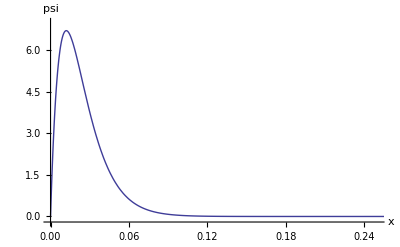

```mathematica
Plot[y[order,1],{x,0,R},AxesLabel->{"x","psi"},PlotRange->{{0,.25},{-0.2,7}},AxesOrigin->{0,-0.2}]
```

We can now view make comparisons between the eigenfunctions generated with the analytical solutions.  We plot the residual of calculated eigenfunction and the analytic solution for the same state, in this case,n =1.  Other states can be check as well:

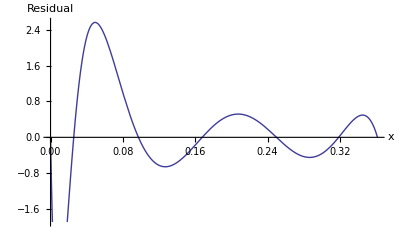

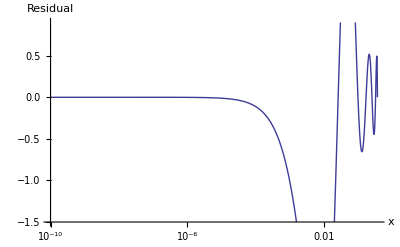

```mathematica
psi[1,0]=2 Z^(3/2) x ⅇ^(-Z x);
psi[2,0]=1/(√2) Z^(3/2) x ⅇ^(-Z x/2) (1-1/2 Z x);
psi[2,1]=1/(2 √6) Z^(5/2) x^2 ⅇ^(-Z x/2);
psi[3,0]=2/(3 √3) Z^(3/2) x ⅇ^(-Z x/3) (1-2/3 Z x+2/27 Z^2 x^2);
psi[3,1]=8/(27 √6) Z^(5/2) x^2 ⅇ^(-Z x/3) (1-1/6 Z x);
psi[3,2]=4/(81 √30) Z^(7/2) x^3 ⅇ^(-Z x/3);
Plot[y[order,1]-psi[1,0],{x,0,R},AxesLabel->{"x","Residual"}]
LogLinearPlot[y[order,1]-psi[1,0],{x,0.0000000001,R},AxesLabel->{"x","Residual"}]
```

And calculate the residuals explcitly as a function of basis order:

```mathematica
residual[i_]:=√NIntegrate[(y[i,1]-psi[1,0])^2,{x,0,R}];
residual[order]
(* Clear[y,i,j, order]; *)
```

0.656368

We can also generate a plot of the residuals as a function of basis order sequentially to track the improvement of accuracy of the Galerkin method (NB. for high orders, this calculation can get quite lengthy since every order is calculated):

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.43909×10^-16 and 2.68479×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.43909×10^-16 and 2.68479×10^-16 for the integral and error estimates.

Greater::nord: Invalid comparison with 0.  + 29529.1\ ⅈ attempted.

Greater::nord: Invalid comparison with 0.  - 1584.19\ ⅈ attempted.

Greater::nord: Invalid comparison with 0.  + 1466.11\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

{1.32665,1.2054,1.04221,0.852652,0.656368,0.472651,0.317113,0.198786,0.117939,0.0670667,0.0364177,0.0186431,0.00894482,0.00403048,0.00171342,0.000703393,0.000264322,0.000096461,0.0000336002,0.0000111958,3.63628×10^-6,1.19068×10^-6,3.07176×10^-6-3.40767 ⅈ,9.65533×10^-6,1.72018×10^-6}

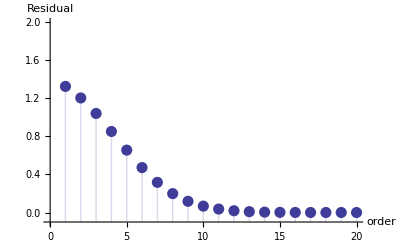

```mathematica
order =25; j=1;

While[j≤order,(galerkinSE[j,0,R,Z,l];residual[j]; j++)];

residuals=Table[residual[i],{i,1,order}]
DiscretePlot[residual[i],{i,1,order},PlotRange->{{0,20},{-0.1,2}},PlotStyle->PointSize[0.02],AxesOrigin->{0,-0.1},AxesLabel->{"order","Residual"}]
```

```mathematica
Clear[y,i,j, order,Z, R, l,galerkinSE];
```

## References

Johnson, W. R., Atomic Structure Theory, Springer-Verlag, Berlin, 2007

Fletcher, C. A. J., Computational Galerkin Methods, Springer-Verlag, Berlin, 1984

Bhatti, M. and Perger, W., J. Phys. B: At. Mol. Opt. Phys. 39 553 (2006)

Johnson, W. R, Blundell, S. A., Sapirstein, J., Phys. Rev. A, 37 307 (1988)